# グラフィックス・プリミティブ

グラフィックスを構成するパーツ

## 平面内のグラフィックス・プリミティブ

```mathematica
Graphics[Point[{1,1}]]
```

-Graphics-

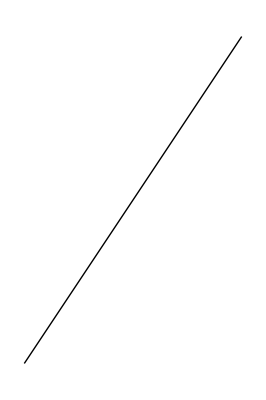

```mathematica
Graphics[
Line[{{1,1},{-1,-2}}]
]
```



```mathematica
Graphics[Circle[{0,0},1]]
```

複数のグラフィックスを描画する：その１「Graphics[{...}]」

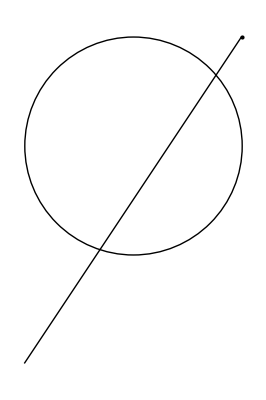

```mathematica
Graphics[
{
Point[{1,1}],
Line[{{1,1},{-1,-2}}],
Circle[{0,0},1]
}
]
```

複数のグラフィックスを描画する：その２「Show」

```mathematica
Show[
Graphics[Point[{1,1}]],
Graphics[Line[{{1,1},{-1,-2}}]],
Graphics[Circle[{0,0},1]]
]
```

-Graphics-

Show コマンドは Plot 系コマンドも描画可能

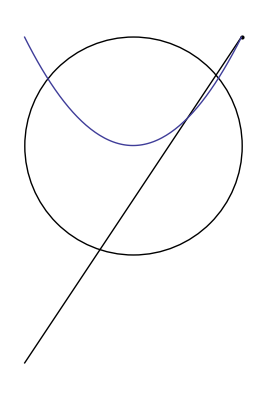

```mathematica
Show[
Graphics[Point[{1,1}]],
Graphics[Line[{{1,1},{-1,-2}}]],
Graphics[Circle[{0,0},1]],
Plot[x^2,{x,-1,1}]
]
```

## 空間内のグラフィックス・プリミティブ

「Graphics」が「Graphics3D」になる．

座標が空間の座標に（３つの数の組）

```mathematica
Graphics3D[Sphere[{0,0,0},1]]
```

-Graphics3D-

## [問題A]

平面内に原点以外の点をひとつ，Graphics コマンドを使って描画しなさい．

```mathematica
Graphics[Point[{1,2}]]
```

-Graphics-

1. で描画した点を原点を中心として π/2だけ回転させた点を描画しなさい．

```mathematica
Graphics[Point[{{Cos[Pi/2],-Sin[Pi/2]},{Sin[Pi/2],Cos[Pi/2]}}.{1,2}]]
```

-Graphics-

1.と2.の２つの点を Show コマンドを使って，一つの平面内に描画しなさい．

```mathematica
Show[
Graphics[Point[{1,2}]],
Graphics[Point[{{Cos[Pi/2],-Sin[Pi/2]},{Sin[Pi/2],Cos[Pi/2]}}.{1,2}]]
]
```

-Graphics-

# Manipulate コマンド

アニメーション，インタラクティブなアプリケーションを作成

次のグラフは a の値によって描画される曲線が異なる．

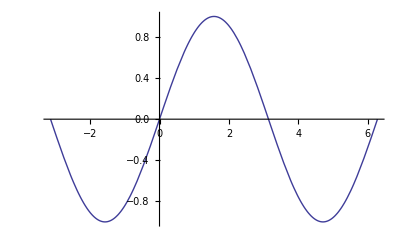

```mathematica
a=0;
Plot[Sin[x-a],{x,-Pi,2*Pi}]
```

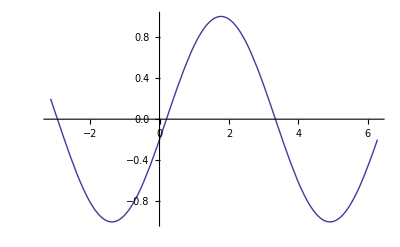

```mathematica
a=0.2;
Plot[Sin[x-a],{x,-Pi,2*Pi}]
```

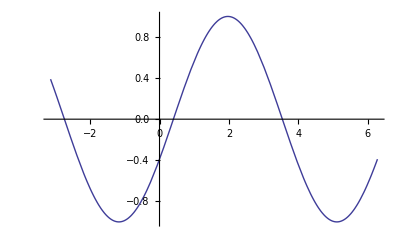

```mathematica
a=0.4;
Plot[Sin[x-a],{x,-Pi,2*Pi}]
```

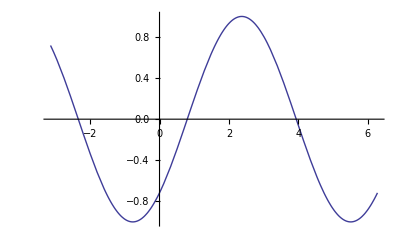

```mathematica
a=0.8;
Plot[Sin[x-a],{x,-Pi,2*Pi}]
```

したがって，a の値を動かせば，曲線が変形（移動）するアニメーションが作れる．

```mathematica
Manipulate[
Plot[Sin[x-a],{x,-Pi,2*Pi}],
{a,0,2*Pi}
]
```

## [問題B]

問題A で作成したグラフィックスにおいて，回転角π/2をパラメーター a に置き換えて，点が原点の周りを回転するアニメーションをつくりなさい

```mathematica
Manipulate[
Show[
Graphics[Circle[{0,0},Sqrt[5]]],
Graphics[Point[{1,2}]],
Graphics[Point[{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}.{1,2}]]
],
{a,0,2*Pi}]
```